```mathematica
eq=y==m*x+c;
eq1=eq/.{x->2,y->3};
eq2=eq/.{x->4,y->5};
s1=Solve[{eq1,eq2},{m,c}]
Simplify[eq/.{m->s1[[1,1,2]],c->s1[[1,1,2]]
}]
```

{{m→1,c→1}}

1+x==y

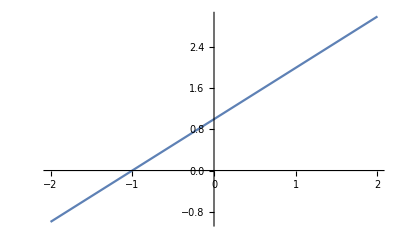

```mathematica
Plot[1+x,{x,-2,2}]
```